## Лабараторная работа номер 6 -Graphics-

```mathematica
(*a)h = 0.1*)(*Определение функции*)
f[x_,y_]:=cos(2x + y) +x -y;
a=0;b=0.3; (*Интервал интегрирования*)
x0=0;y0= 1; (*Начальные условия*)
h1=0.1; (*Шаг*)
n1=Floor[(b-a)/h1]; (*Количество шагов*)
(*Инициализация решения*)
solEulerCauchy={{x0,y0}};
x=x0;y=y0;
(*Цикл для метода Эйлера-Коши*)
For[k=1,k<=n1,k++,
(*Вычисление предиктора*)
yPr=y+h1*f[x,y];
(*Вычисление корректора*)
y=y+h1/2*(f[x,y]+f[x+h1,yPr]);
(*Обновление значения x*)
x=x+h1;
solEulerCauchy=Append[solEulerCauchy,{x,y}]]

solEulerCauchy//TableForm
```

0 | 1
0.1 | 1+0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)
0.2 | 1+0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)+0.05 (-1.7-0.1 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)+cos (1.2+0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos))-0.1 (-0.9-0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)+cos (1.2+0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)))+cos (1.4+0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)+0.1 (-0.9-0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)+cos (1.2+0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)))))
0.3 | 1+0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)+0.05 (-1.7-0.1 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)+cos (1.2+0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos))-0.1 (-0.9-0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)+cos (1.2+0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)))+cos (1.4+0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)+0.1 (-0.9-0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)+cos (1.2+0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)))))+0.05 (-1.5-0.1 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)-0.1 (-1.7-0.1 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)+cos (1.2+0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos))-0.1 (-0.9-0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)+cos (1.2+0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)))+cos (1.4+0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)+0.1 (-0.9-0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)+cos (1.2+0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)))))+cos (1.4+0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)+0.05 (-1.7-0.1 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)+cos (1.2+0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos))-0.1 (-0.9-0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)+cos (1.2+0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)))+cos (1.4+0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)+0.1 (-0.9-0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)+cos (1.2+0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos))))))-0.1 (-0.8-0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)-0.05 (-1.7-0.1 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)+cos (1.2+0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos))-0.1 (-0.9-0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)+cos (1.2+0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)))+cos (1.4+0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)+0.1 (-0.9-0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)+cos (1.2+0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)))))+cos (1.4+0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)+0.05 (-1.7-0.1 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)+cos (1.2+0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos))-0.1 (-0.9-0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)+cos (1.2+0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)))+cos (1.4+0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)+0.1 (-0.9-0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)+cos (1.2+0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)))))))+cos (1.6+0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)+0.05 (-1.7-0.1 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)+cos (1.2+0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos))-0.1 (-0.9-0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)+cos (1.2+0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)))+cos (1.4+0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)+0.1 (-0.9-0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)+cos (1.2+0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)))))+0.1 (-0.8-0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)-0.05 (-1.7-0.1 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)+cos (1.2+0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos))-0.1 (-0.9-0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)+cos (1.2+0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)))+cos (1.4+0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)+0.1 (-0.9-0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)+cos (1.2+0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)))))+cos (1.4+0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)+0.05 (-1.7-0.1 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)+cos (1.2+0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos))-0.1 (-0.9-0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)+cos (1.2+0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)))+cos (1.4+0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)+0.1 (-0.9-0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)+cos (1.2+0.05 (-1.9-0.1 (-1+cos)+cos+(1.2+0.1 (-1+cos)) cos)))))))))

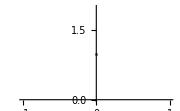

```mathematica
gr1=ListPlot[solEulerCauchy,ImageSize->Small]
```

```mathematica
Clear[x];Clear[y];
```

```mathematica
(*А)h=0,05*)
```

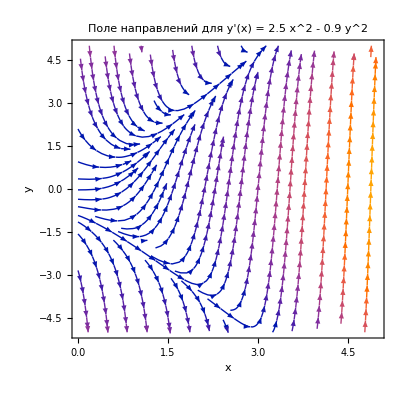

0 | 0.4
0.05 | 0.393085
0.1 | 0.387029
0.15 | 0.382415
0.2 | 0.379805
0.25 | 0.379745
0.3 | 0.382764
0.35 | 0.389372
0.4 | 0.400055
0.45 | 0.415276
0.5 | 0.435462
0.55 | 0.461003
0.6 | 0.492241
0.65 | 0.529463
0.7 | 0.572885
0.75 | 0.622651
0.8 | 0.678816
0.85 | 0.741348
0.9 | 0.810112
0.95 | 0.884881
1. | 0.965327

```mathematica
f[x_,y_]:=2.5 x^2-0.9 y^2;
f[x_,y_]:=2.5 x^2-0.9 y^2;

(*Построение поля направлений*)
StreamPlot[{1,f[x,y]},{x,0,5},{y,-5,5},PlotLabel->"Поле направлений для y'(x) = 2.5 x^2 - 0.9 y^2",AxesLabel->{"x","y"},StreamStyle->Arrowheads[0.03]]


a=0;b=1; (*Интервал интегрирования*)
x0=0;y0=0.4; (*Начальные условия*)
h2=0.05; (*Шаг*)
n2=Floor[(b-a)/h2]; (*Количество шагов*)
(*Инициализация решения*)
solEulerCauchy={{x0,y0}};
x=x0;y=y0;
(*Цикл для метода Эйлера-Коши*)
For[k=1,k<=n2,k++,
(*Вычисление предиктора*)
yPr=y+h2*f[x,y];
(*Вычисление корректора*)
y=y+h2/2*(f[x,y]+f[x+h2,yPr]);
(*Обновление значения x*)
x=x+h2;
solEulerCauchy=Append[solEulerCauchy,{x,y}]]

solEulerCauchy//TableForm
```

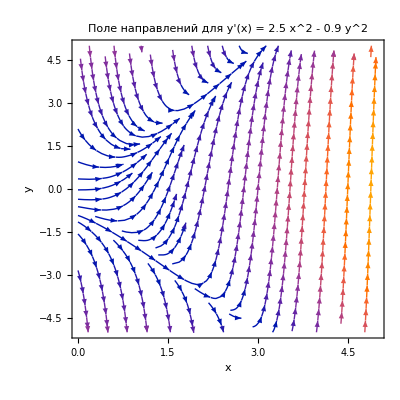

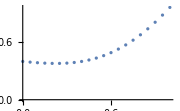

```mathematica
gr2=ListPlot[solEulerCauchy,ImageSize->Small]
```

```mathematica
Clear[x];Clear[y];

(*Б)h=0.1*)
```

```mathematica
f[x_,y_]=cos(2x + y) +x -y;
a=0;b=0.2;
x0=0;y0=1;
h1=0.1;
n1=Floor[(b-a)/h1];
(*Цикл для итераций метода 
Рунге-Кутты четвертого порядка*)
sol1={{x0,y0}};
x=x0;y=y0;
For[k=1,k<n1+1,k++,
(*Вычисление коэффициентов k — оценка 
производных на интервале*)
k1=h1*f[x,y];
k2=h1*f[x+h1/2,y+k1/2];
k3=h1*f[x+h1/2,y+k2/2];
k4=h1*f[x+h1,y+k3];
x=x+h1;
y=y+(k1+2*k2+2*k3+k4)/6;
sol1=Append[sol1,{x,y}]]

sol1//TableForm
```

```mathematica
gr3=ListPlot[sol1,ImageSize->Small]
```

-Graphics-

```mathematica
Clear[x];Clear[y];
```

```mathematica
(*Б)h=0.05*)
```

```mathematica
f[x_,y_]=cos(2x + y) +x -y;
a=0;b= 0.5;
x0=0;y0=1;
h2=0.05;
n2=Floor[(b-a)/h2];
sol2={{x0,y0}};
x=x0;y=y0;
For[k=1,k<n2+1,k++,
k1=h2*f[x,y];
k2=h2*f[x+h2/2,y+k1/2];
k3=h2*f[x+h2/2,y+k2/2];
k4=h2*f[x+h2,y+k3];
x=x+h2;
y=y+(k1+2*k2+2*k3+k4)/6;
sol2=Append[sol2,{x,y}]]

sol2//TableForm
```

0 | 1
0.05 | 1+0.05 (-0.9-0.1 (-0.95-0.05 (-1+cos)+(1.1+0.05 (-1+cos)) cos)+cos (1.2+0.1 (-0.95-0.05 (-1+cos)+(1.1+0.05 (-1+cos)) cos)))
0.1 | 1+0.1 (-0.9-0.1 (-0.95-0.05 (-1+cos)+(1.1+0.05 (-1+cos)) cos)+cos (1.2+0.1 (-0.95-0.05 (-1+cos)+(1.1+0.05 (-1+cos)) cos)))
0.15 | 1+0.15 (-0.9-0.1 (-0.95-0.05 (-1+cos)+(1.1+0.05 (-1+cos)) cos)+cos (1.2+0.1 (-0.95-0.05 (-1+cos)+(1.1+0.05 (-1+cos)) cos)))
0.2 | 1+0.2 (-0.9-0.1 (-0.95-0.05 (-1+cos)+(1.1+0.05 (-1+cos)) cos)+cos (1.2+0.1 (-0.95-0.05 (-1+cos)+(1.1+0.05 (-1+cos)) cos)))
0.25 | 1+0.25 (-0.9-0.1 (-0.95-0.05 (-1+cos)+(1.1+0.05 (-1+cos)) cos)+cos (1.2+0.1 (-0.95-0.05 (-1+cos)+(1.1+0.05 (-1+cos)) cos)))
0.3 | 1+0.3 (-0.9-0.1 (-0.95-0.05 (-1+cos)+(1.1+0.05 (-1+cos)) cos)+cos (1.2+0.1 (-0.95-0.05 (-1+cos)+(1.1+0.05 (-1+cos)) cos)))
0.35 | 1+0.35 (-0.9-0.1 (-0.95-0.05 (-1+cos)+(1.1+0.05 (-1+cos)) cos)+cos (1.2+0.1 (-0.95-0.05 (-1+cos)+(1.1+0.05 (-1+cos)) cos)))
0.4 | 1+0.4 (-0.9-0.1 (-0.95-0.05 (-1+cos)+(1.1+0.05 (-1+cos)) cos)+cos (1.2+0.1 (-0.95-0.05 (-1+cos)+(1.1+0.05 (-1+cos)) cos)))
0.45 | 1+0.45 (-0.9-0.1 (-0.95-0.05 (-1+cos)+(1.1+0.05 (-1+cos)) cos)+cos (1.2+0.1 (-0.95-0.05 (-1+cos)+(1.1+0.05 (-1+cos)) cos)))
0.5 | 1+0.5 (-0.9-0.1 (-0.95-0.05 (-1+cos)+(1.1+0.05 (-1+cos)) cos)+cos (1.2+0.1 (-0.95-0.05 (-1+cos)+(1.1+0.05 (-1+cos)) cos)))

```mathematica
gr4=ListPlot[sol2,ImageSize->Small]
```

-Graphics-

```mathematica
(*В)*)
```

```mathematica
Clear[x];Clear[y];
```

```mathematica
dsol=DSolve[{y'[x]==f[x,y[x]],y[x0]==y0},y[x],x]
y1[x_]=y[x]/.Flatten[dsol];
gr5=Plot[y1[x],{x,0,1}]
```

{{y[x]→1.-0.81 x+1.01 cos x+0.095 cos^2 x+0.005 cos^3 x}}

-Graphics-

{{y[x]→InterpolatingFunction[…][x]}}

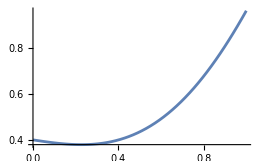

```mathematica
ndsol=NDSolve[{y'[x]==f[x,y[x]],y[x0]==y0},y[x],{x,0,1}]
y1[x_]=y[x]/.Flatten[ndsol];
gr6=Plot[y1[x],{x,0,1}]
```

```mathematica
Show[gr1,gr3](*h=0.1*)
Show[gr2,gr4](*h=0.05*)
```

Show::gcomb: Could not combine the graphics objects in Show[gr1,ListPlot[sol1,ImageSize→Small]].

Show[gr1,ListPlot[sol1,ImageSize→Small]]

Show::gcomb: Could not combine the graphics objects in Show[gr2,].

Show[gr2,-Graphics-]

```mathematica
gr2 
gr4
```

gr2

-Graphics-

```mathematica
ClearAll
```

ClearAll

```mathematica
(*А)*)
```

```mathematica
(*Определение функции*)
f[x_,y_]:=cos(2x + y) +x -y;

(*Параметры задачи*)
a=0;b=0.5; (*Интервал интегрирования*)
x0=0;y0= 1; (*Начальные условия*)
h=0.1; (*Шаг*)
n=Floor[(b-a)/h]; (*Количество шагов*)

(*Инициализация решения*)
solEulerCauchy={{x0,y0}};
x=x0;y=y0;

(*Цикл для метода Эйлера-Коши*)
For[k=1,k<=n,k++,(*Вычисление предиктора*)yPredictor=y+h*f[x,y];
(*Вычисление корректора*)y=y+h/2*(f[x,y]+f[x+h,yPredictor]);
(*Обновление значения x*)x=x+h;
(*Сохранение результата*)solEulerCauchy=Append[solEulerCauchy,{x,y}]]

(*Вывод таблицы значений*)
solEulerCauchy//TableForm
```

```mathematica
(*ListPlot[solEulerCauchy,Joined->True,PlotStyle->Blue,PlotLabel->"Модифицированный метод Эйлера (Эйлера-Коши)"]*)
```

```mathematica
gr4=ListPlot[solEulerCauchy,ImageSize->Small]
```

-Graphics-

```mathematica
ClearAll
```

ClearAll

```mathematica
(*Определение функции*)
f[x_,y_]:=cos(2x + y) +x -y;

(*Параметры задачи*)
a=0;b=0.5; (*Интервал интегрирования*)
x0=0;y0=0; (*Начальные условия*)
h=0.05; (*Шаг*)
n=Floor[(b-a)/h]; (*Количество шагов*)

(*Инициализация решения*)
solEulerCauchy={{x0,y0}};
x=x0;y=y0;

(*Цикл для метода Эйлера-Коши*)
For[k=1,k<=n,k++,(*Вычисление предиктора*)yPredictor=y+h*f[x,y];
(*Вычисление корректора*)y=y+h/2*(f[x,y]+f[x+h,yPredictor]);
(*Обновление значения x*)x=x+h;
(*Сохранение результата*)solEulerCauchy=Append[solEulerCauchy,{x,y}]]

(*Вывод таблицы значений*)
solEulerCauchy//TableForm
```

0 | 0.4
0.05 | 0.393085
0.1 | 0.387029
0.15 | 0.382415
0.2 | 0.379805
0.25 | 0.379745
0.3 | 0.382764
0.35 | 0.389372
0.4 | 0.400055
0.45 | 0.415276
0.5 | 0.435462
0.55 | 0.461003
0.6 | 0.492241
0.65 | 0.529463
0.7 | 0.572885
0.75 | 0.622651
0.8 | 0.678816
0.85 | 0.741348
0.9 | 0.810112
0.95 | 0.884881
1. | 0.965327

```mathematica
gr4=ListPlot[solEulerCauchy,ImageSize->Small]
```

-Graphics-

```mathematica
(*Для более точных расчетов и при большем шаге предпочтителен метод Рунге-Кутты или NDSolve.Уменьшение шага
h значительно повышает точность метода Эйлера-Коши.*)
```

```mathematica
ClearAll
```

ClearAll

```mathematica
(*22222222222222222222*)
-Graphics-
```

```mathematica
(*Определение функции f1 и f2 для системы уравнений*)
f1[x_,y_,z_] := -2z;
f2[x_,y_,z_] := -5;

(*Начальные условия*)
x0=0;
y0=0;
z0=0;

(*Шаг*)
h=0.1;

(*Количество шагов*)
n=Floor[(1-x0)/h];

(*Инициализация списка для хранения решений*)
sol={{x0,y0,z0}};

(*Итерация по методу Эйлера*)
For[k=1,k<=n,k++,(*Извлечение текущих значений*){x,y,z}=sol[[-1]];
(*Вычисление значений для k1 и k2*)k1y=h f1[x,y,z];
k1z=h f2[x,y,z];
k2y=h f1[x+h/2,y+k1y/2,z+k1z/2];
k2z=h f2[x+h/2,y+k1y/2,z+k1z/2];
(*Обновление значений y и z*)newY=y+k2y;
newZ=z+k2z;
(*Добавление новых значений в список*)sol=Append[sol,{x+h,newY,newZ}];];

(*Вывод полученных решений в виде таблицы*)
sol//TableForm
```

0 | 0 | 0
0.1 | 0.05 | -0.5
0.2 | 0.2 | -1.
0.3 | 0.45 | -1.5
0.4 | 0.8 | -2.
0.5 | 1.25 | -2.5
0.6 | 1.8 | -3.
0.7 | 2.45 | -3.5
0.8 | 3.2 | -4.
0.9 | 4.05 | -4.5
1. | 5. | -5.

```mathematica
(*Построение графика для y(x)*)ListLinePlot[sol[[All,{1,2}]],PlotLabels->{"x","y"},PlotStyle->Blue,AxesLabel->{"x","y"}]

(*Построение графика для z(x)*)
ListLinePlot[sol[[All,{1,3}]],PlotLabels->{"x","z"},PlotStyle->Red,AxesLabel->{"x","z"}]
```

-Graphics-

-Graphics-

```mathematica
(*Построение 3D-графика для x,y(x),z(x)*)ListLinePlot3D[Transpose[{sol[[All,1]],sol[[All,2]],sol[[All,3]]}],PlotLabels->{"x","y(x)","z(x)"},AxesLabel->{"x","y","z"},PlotStyle->{Blue},Mesh->All]
```

-Graphics3D-

```mathematica
ClearAll
```

```mathematica
ClearAll
```

ClearAll

```mathematica
(*Определение функций для правых частей уравнений*)
f1[x_,y_,z_] := -2z;
f2[x_,y_,z_] := -5;


(*Начальные условия*)
x0=0;
y0=0;
z0=0;

(*Шаг*)
h=0.1;

(*Количество шагов*)
n=Floor[(1-x0)/h];

(*Инициализация списка для хранения решений*)
sol={{x0,y0,z0}};

(*Итерация по методу Рунге-Кутты*)
For[k=1,k<=n,k++,(*Извлечение текущих значений*){x,y,z}=sol[[-1]];
(*Вычисление значений для k1,k2,k3,k4 для y и z*)k1y=h f1[x,y,z];
k1z=h f2[x,y,z];
k2y=h f1[x+h/2,y+k1y/2,z+k1z/2];
k2z=h f2[x+h/2,y+k1y/2,z+k1z/2];
k3y=h f1[x+h/2,y+k2y/2,z+k2z/2];
k3z=h f2[x+h/2,y+k2y/2,z+k2z/2];
k4y=h f1[x+h,y+k3y,z+k3z];
k4z=h f2[x+h,y+k3y,z+k3z];
(*Обновление значений y и z*)newY=y+(k1y+2 k2y+2 k3y+k4y)/6;
newZ=z+(k1z+2 k2z+2 k3z+k4z)/6;
(*Добавление новых значений в список*)sol=Append[sol,{x+h,newY,newZ}];];

(*Вывод полученных решений в виде таблицы*)
sol//TableForm
```

0 | 0 | 0
0.1 | 0.05 | -0.5
0.2 | 0.2 | -1.
0.3 | 0.45 | -1.5
0.4 | 0.8 | -2.
0.5 | 1.25 | -2.5
0.6 | 1.8 | -3.
0.7 | 2.45 | -3.5
0.8 | 3.2 | -4.
0.9 | 4.05 | -4.5
1. | 5. | -5.

```mathematica
(*Построение графика для y(x)*)ListLinePlot[sol[[All,{1,2}]],PlotLabels->{"x","y"},PlotStyle->Blue,AxesLabel->{"x","y"}]

(*Построение графика для z(x)*)
ListLinePlot[sol[[All,{1,3}]],PlotLabels->{"x","z"},PlotStyle->Red,AxesLabel->{"x","z"}]
```

-Graphics-

-Graphics-

```mathematica
ClearAll
```

```mathematica
ClearAll
```

ClearAll

```mathematica
(*Определение функций f и gf[x_,y_,z_]:=(*ваша функция f здесь*)
g[x_,y_,z_]:=(*ваша функция g здесь*)
x0=0;  
y0=3;  (*Начальное значение y*)
z0=1;  (*Начальное значение z*)

(*Решение системы уравнений*)
sol3=DSolve[{y'[x]==f[x,y[x],z[x]],z'[x]==g[x,y[x],z[x]],y[x0]==y0,z[x0]==z0},{y,z},x];

(*Получение функций y и z из решения*)
y1[x_]=y[x]/. First[sol3];
z1[x_]=z[x]/. First[sol3];

(*Пример использования функций y1 и z1*)
Plot[{y1[x],z1[x]},{x,0,1},PlotLegends->{"y(x)","z(x)"},AxesLabel->{"x","y, z"},PlotLabel->"Решение системы дифференциальных уравнений"]*)
```

```mathematica
f[x_,y_,z_] := -2z;
g[x_,y_,z_] := -5;

(*Начальные условия*)
x0=0;
y0=0; (*Начальное значение y*)
z0=0; (*Начальное значение z*)
(*Решение системы уравнений*)
sol3=DSolve[{y'[x]==f[x,y[x],z[x]],z'[x]==g[x,y[x],z[x]],y[x0]==y0,z[x0]==z0},{y,z},x];
(*Получение функций y и z из решения*)
y1[x_]=y[x]/. First[sol3];
z1[x_]=z[x]/. First[sol3];
(*Получение функций y и z из решения*)
y1[x_]=y[x]/. First[sol3];
z1[x_]=z[x]/. First[sol3];

(*Пример использования функций y1 и z1*)
Plot[{y1[x],z1[x]},{x,0,1},PlotLegends->{"y(x)","z(x)"},AxesLabel->{"x","y, z"},PlotLabel->"Решение системы дифференциальных уравнений"]
```

DSolve::dsvar: 0.9 cannot be used as a variable.

ReplaceAll::reps: {0==-2 (-4.5)[0.9],False,4.05[0]==0,(-4.5)[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {0.==-2. (-4.5)[0.9],False,4.05[0.]==0.,(-4.5)[0.]==0.} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-